```mathematica
F={10^3,10^4,10^5,10^6,3 10^6,5 10^6,7 10^6,8 10^6,9 10^6,10^7,1.5 10^7}/10^4;
Δx={2.75 10^-4,2.75 10^-3,2.75 10^-2,0.275,0.827,1.3748,1.9247,2.1997,2.4746,2.837,4.56};
σ={3.6 10^5,3.6 10^6,3.6 10^7,3.6 10^8,1.14 10^9,1.86 10^9,2.6 10^9,2.97 10^9,3.346 10^9,4.43 10^9,7.6 10^9}/10^6;
```

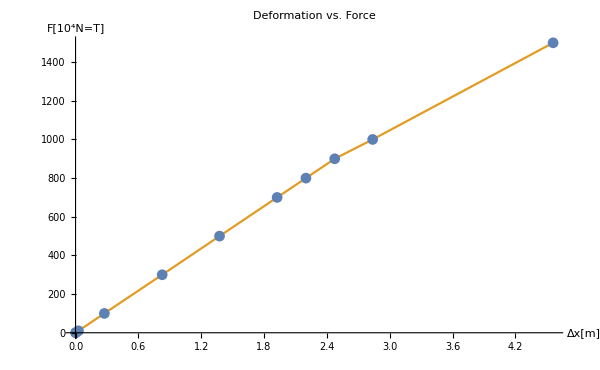

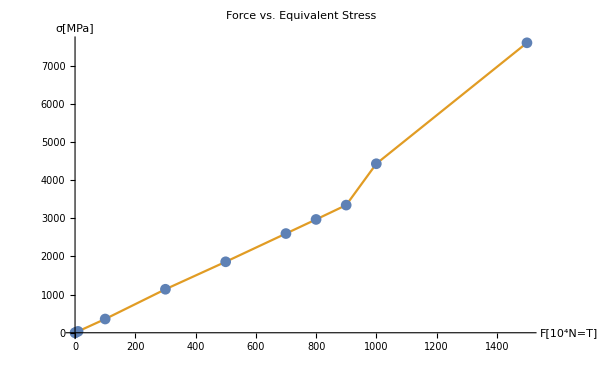

H:\Version\git\ag\ansys\luka_fender

Export::noopen: Cannot open "deformation.pdf".

$Failed

equivalent_stress.pdf

```mathematica
pl1=ListPlot[{Transpose[{Δx,F}],Transpose[{Δx,F}]},Joined->{False,True},
AxesLabel->{"Δx[m]","F[10^4N=T]"},
PlotLabel->"Deformation vs. Force"
]
pl2=ListPlot[{Transpose[{F,σ}],Transpose[{F,σ}]},Joined->{False,True},
AxesLabel->{"F[10^4N=T]","σ[MPa]"},
PlotLabel->"Force vs. Equivalent Stress"]
SetDirectory[NotebookDirectory[]]
Export["deformation.pdf",pl1]
Export["equivalent_stress.pdf",pl2]
```

```mathematica
line = Fit[Transpose[{Δx⟦1;;9⟧,F⟦1;;9⟧}], {1,x},x]
```

-0.107586+363.711 x

```mathematica
k=363.71;
m=39433; (* [kg] *)
v=0.05; (* m/s *)
ω=Sqrt[k/m];
x[t_]:=v/ω Sin[ω t];
```

1.73027×10^6

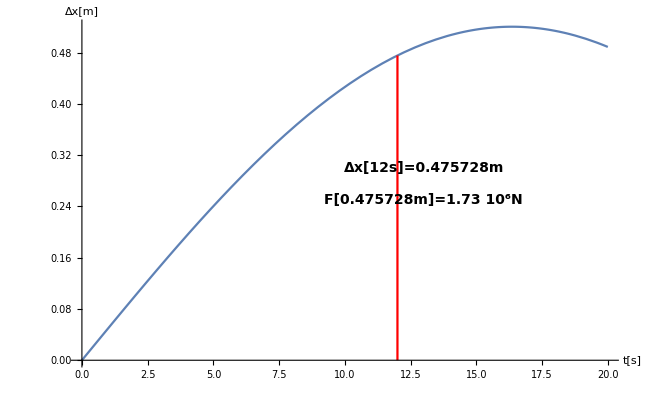

```mathematica
fx=line/.x->x[12]*10^4//N
p1=Plot[x[t],{t,0,20},
AxesLabel->{"t[s]","Δx[m]"}
];
p2=ListPlot[{{12,0},{12,x[12]}},Joined->True,PlotStyle->Red];
pp=Show[p1,p2,
Graphics[Text[StyleForm["Δx[12s]="<>ToString[x[12]]<>"m",FontSize->14,FontWeight->"Bold"],{13,0.3}]],
Graphics[Text[StyleForm["F["<>ToString[x[12]]<>"m]=1.73 10^6N",FontSize->14,FontWeight->"Bold"],{13,0.25}]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["odmik_cas.pdf",pp]
```

H:\Version\git\ag\ansys\luka_fender

odmik_cas.pdf

```mathematica
line/.x->x[12]*10^4
```

1.73027×10^6